# Thevenin' s Theorem

Charlie Bushman
Phys 235 Lab #3
04-23-19

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
δQ[f_,p_,δ_]:=Sqrt[Sum[(D[f,p[[i]]] δ[[i]])^2,{i,1,Length[p]}]];
```

This is a Mathematica notebook detailing the analysis of Lab 03 of Carleton College Phys 235. In this lab, we seek to experimentally verify Thevenin’s theorem with a couple circuits of varying complexities. The third section will be focused on using our (hopefully) verified theorem to find the effective resistance of a function generator.
Throughout this lab we will be making use of a circuit that we will call “rest of the world” or the “observer”. It will measure the voltage across two terminals and can measure the current through the resistor, R_s, because the voltmeter is assumed to have R→∞.

```mathematica
(*Note that these file paths will have to change if this isn't on my computer*)
Import["/home/ctbus/Pictures/Selection_004.png"]
```

-Graphics-

## Section A

In Section A, we are focusing on a simple circuit with just one battery and one resistor. We will attach the observer circuit to this simple circuit and measure the voltage when the load resistor goes to infinity (is not attached). This voltage is the Thevenin voltage of the simple circuit. The Thevenin resistance is V_th / I_ab where I_ab is the current through the load resistor when it has resistance of zero. To get this, we will measure the voltage (because voltmeters are more reliable than ammeters) for varying load resistances. We can then calculate the current from this and plot voltage vs current. The linearization should give us a y-intercept of the current when the load resistor goes to zero.

```mathematica
voltResist={{75.25,15.3},{152.95,30.3},{363.6,75.3},{708.9,150.3},{1333.0,300.3},{2788,750.3}};
(*The factors of 1000 on the resitances here and for δI are added to compensate for the voltages being mV instead of V*)
f[x_]:={x[[1]],x[[1]]/(1000*x[[2]])};
voltCurr=Map[f,voltResist];
voltCurr//TableForm
δV={0.04,0.04,0.1,0.1,0.1,1};
δRs={0.153,0.303,0.753,1.503,3.003,7.503};
δI=Table[Sqrt[(1/(1000*voltResist[[x,2]]) δV[[x]])^2+((-voltResist[[x,1]])/(1000*voltResist[[x,2]]^2) δRs[[x]])^2],{x,1,Length[δV]}];
```

75.25 | 0.0049183
152.95 | 0.00504785
363.6 | 0.00482869
708.9 | 0.00471657
1333. | 0.00443889
2788 | 0.00371585

{0.00502639-4.27373×10^-7 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00502639 | 0.0000463765 | 108.382 | 4.34584×10^-8
x | -4.27373×10^-7 | 1.11756×10^-7 | -3.82417 | 0.0187113}

2023.32 Ω±18.7741 Ω

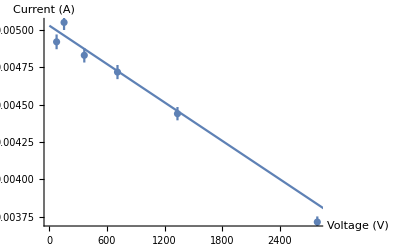

```mathematica
fit=LinearModelFit[voltCurr,x,x,Weights->1/(δV^2+δI^2)];
fit[{"BestFit","ParameterTable"}]
Ith=fit[[1,2,1]];
δVth=0.01;
δIth=0.0000463765;
Vth=10.17;
Rth=Vth/Ith;
δRth=Sqrt[(1/Ith δVth)^2+(-Vth/Ith^2 δIth)^2];
Rth "Ω" ± δRth "Ω"
Show[ErrorListPlot[Table[{{voltCurr[[i,1]],voltCurr[[i,2]]},ErrorBar[δV[[i]],δI[[i]]]},{i,1,Length[voltCurr]}]],Plot[fit[x],{x,0,3000}],AxesLabel->{"Voltage (V)","Current (A)"},ImageSize->Full]
```

Our theoretical values are V_th = V_0 = 10.2 V ± 0.2 V and R_th = R_0 = 2 kΩ ± 0.02 kΩ. Our experimental value for the Thevenin voltage came out to V_th = 10.17 V ± 0.01 V and for the Thevenin resistance came out to R_th = 2.02 kΩ ± 0.02 kΩ, both of which are within theoretical bounds of their theoretical counterparts.

## Section B

In Section B, we proceed with the same experiment but with a more complicated circuit. The circuit (seen below) is attached with our observer over terminals A and B and then over B and C. We will again be trying to verify that our experimental values for Thevenin equivalent voltages and resitances come out the same as theory.

```mathematica
Import["/home/ctbus/Pictures/Selection_005.png"]
```

-Graphics-

### Section A .1: Observing over AB Terminals

```mathematica
voltResist={{0.2114,15.3},{0.4131,30.3},{0.9708,75.3},{1.7943,150.3},{3.072,300.3},{5.337,750.3}};
f[x_]:={x[[1]],x[[1]]/x[[2]]};
voltCurr=Map[f,voltResist];
voltCurr//TableForm
δV={0.0001,0.0001,0.0001,0.0002,0.001,0.001};
δRs={0.153,0.303,0.753,1.503,3.003,7.503};
δI=Table[Sqrt[(1/voltResist[[x,2]] δV[[x]])^2+((-voltResist[[x,1]])/voltResist[[x,2]]^2 δRs[[x]])^2],{x,1,Length[δV]}];
```

0.2114 | 0.013817
0.4131 | 0.0136337
0.9708 | 0.0128924
1.7943 | 0.0119381
3.072 | 0.0102298
5.337 | 0.00711315

{0.0141223-0.00125363 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0141223 | 0.0000347793 | 406.055 | 2.20697×10^-10
x | -0.00125363 | 0.0000331695 | -37.7945 | 2.92694×10^-6}

429.817 Ω±14.2015 Ω

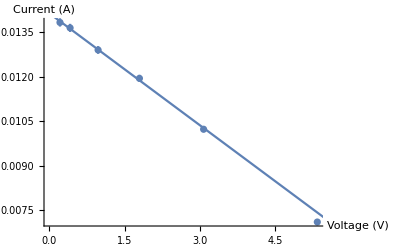

```mathematica
fit=LinearModelFit[voltCurr,x,x,Weights->1/(δV^2+δI^2)];
fit[{"BestFit","ParameterTable"}]
Ith=fit[[1,2,1]];
δVth=0.2;
δIth=0.0000347793;
Vth=6.07;
Rth=Vth/Ith;
δRth=Sqrt[(1/Ith δVth)^2+(-Vth/Ith^2 δIth)^2];
Rth "Ω" ± δRth "Ω"
Show[ErrorListPlot[Table[{{voltCurr[[i,1]],voltCurr[[i,2]]},ErrorBar[δV[[i]],δI[[i]]]},{i,1,Length[voltCurr]}]],Plot[fit[x],{x,0,3000}],
AxesLabel->{"Voltage (V)","Current (A)"},ImageSize->Full]
```

```mathematica
Clear[R1,R2,R345,R3,R4,R5,V0,δR1,δR2,δR345,δR3,δR4,δR5,δV0]
Itheor=V0/(R1+R2+R345);δItheor=δQ[Itheor,{V0,R1,R2,R345},{δV0,δR1,δR2,δR345}];
Vtheor=Itheor R345;
Clear[Itheor]
δVtheor=δQ[Vtheor,{Itheor,R345},{δItheor,δR345}];
Rtheor=(1/R345+1/(R1+R2))^-1;δRtheor=δQ[Rtheor,{R345,R1,R2},{δR345,δR1,δR2}];
```

```mathematica
V0=37.0;R1=1000;R2=2000;R345=(1/R3+1/R4+1/R5)^-1;
δV0=0.2;δR1=10;δR2=20;δR345=δQ[R345,{R3,R4,R5},{δR3,δR4,δR5}];
R3=5000;R4=2000;R5=1000;δR3=50;δR4=20;δR5=10;
Vtheor "V" ± δVtheor "V"
(Rtheor//N) "Ω" ± (δRtheor//N) "Ω"
```

6.06557 V±0.0338812 V

491.803 Ω±2.81208 Ω

### Section A .2: Observing over BC Terminals

```mathematica
voltResist={{0.3465,15.3},{0.6966,30.3},{1.6125,75.3},{3.019,150.3},{5.319,300.3},{9.622,750.3}};
f[x_]:={x[[1]],x[[1]]/x[[2]]};
voltCurr=Map[f,voltResist];
voltCurr//TableForm
δV={0.0001,0.0001,0.0002,0.001,0.001,0.001};
δRs={0.153,0.303,0.753,1.503,3.003,7.503};
δI=Table[Sqrt[(1/voltResist[[x,2]] δV[[x]])^2+((-voltResist[[x,1]])/voltResist[[x,2]]^2 δRs[[x]])^2],{x,1,Length[δV]}];
```

0.3465 | 0.0226471
0.6966 | 0.0229901
1.6125 | 0.0214143
3.019 | 0.0200865
5.319 | 0.0177123
9.622 | 0.0128242

{0.0233229-0.00108264 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0233229 | 0.000196707 | 118.566 | 3.03459×10^-8
x | -0.00108264 | 0.000104029 | -10.4072 | 0.000481451}

898.26 Ω±7.58813 Ω

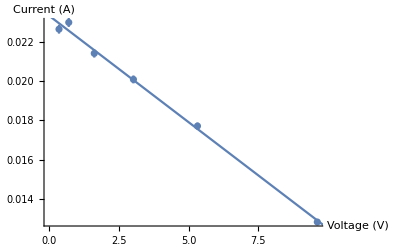

```mathematica
fit=LinearModelFit[voltCurr,x,x,Weights->1/(δV^2+δI^2)];
fit[{"BestFit","ParameterTable"}]
Ith=fit[[1,2,1]];
δVth=0.01;
δIth=0.000196707;
Vth=20.95;
Rth=Vth/Ith;
δRth=Sqrt[(1/Ith δVth)^2+(-Vth/Ith^2 δIth)^2];
Rth "Ω" ± δRth "Ω"
Show[ErrorListPlot[Table[{{voltCurr[[i,1]],voltCurr[[i,2]]},ErrorBar[δV[[i]],δI[[i]]]},{i,1,Length[voltCurr]}]],Plot[fit[x],{x,0,3000}],AxesLabel->{"Voltage (V)","Current (A)"},ImageSize->Full]
```

```mathematica
Clear[R1,R2,R345,R3,R4,R5,V0,δR1,δR2,δR345,δR3,δR4,δR5,δV0]
Itheor=V0/(R1+R2+R345);δItheor=δQ[Itheor,{V0,R1,R2,R345},{δV0,δR1,δR2,δR345}];
Vtheor=Itheor R2;
Clear[Itheor]
δVtheor=δQ[Vtheor,{Itheor,R2},{δItheor,δR2}];
Rtheor=(1/(R1+R345)+1/R2)^-1;δRtheor=δQ[Rtheor,{R345,R1,R2},{δR345,δR1,δR2}];
```

```mathematica
V0=37.0;R1=1000;R2=2000;R345=(1/R3+1/R4+1/R5)^-1;
δV0=0.2;δR1=10;δR2=20;δR345=δQ[R345,{R3,R4,R5},{δR3,δR4,δR5}];
R3=5000;R4=2000;R5=1000;δR3=50;δR4=20;δR5=10;
Vtheor "V" ± δVtheor "V"
(Rtheor//N) "Ω" ± (δRtheor//N)"Ω"
```

20.623 V±0.0912819 V

885.246 Ω±5.14736 Ω

## Section C

In this section, we will be using Thevenin’s theorem to determine the resistance of our function generator. The function generator produces an EMF so it should also have an internal resistance that would be helpful to know in future labs using it.

```mathematica
voltResist={{0.1855,15.3},{0.3006,30.3},{0.4797,75.3},{0.6015,150.3},{0.6875,300.3},{0.7505,750.3}};
f[x_]:={x[[1]],x[[1]]/x[[2]]};
voltCurr=Map[f,voltResist];
voltCurr//TableForm
δV={0.0001,0.0001,0.0001,0.0001,0.0001,0.0001};
δRs={0.153,0.303,0.753,1.503,3.003,7.503};
δI=Table[Sqrt[(1/voltResist[[x,2]] δV[[x]])^2+((-voltResist[[x,1]])/voltResist[[x,2]]^2 δRs[[x]])^2],{x,1,Length[δV]}]
```

0.1855 | 0.0121242
0.3006 | 0.00992079
0.4797 | 0.00637052
0.6015 | 0.004002
0.6875 | 0.00228938
0.7505 | 0.00100027

{0.000121418,0.0000992628,0.000063719,0.0000400255,0.0000228962,0.0000100036}

{0.0158222-0.0197039 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0158222 | 0.0000432552 | 365.787 | 3.35131×10^-10
x | -0.0197039 | 0.0000732508 | -268.992 | 1.14592×10^-9}

50.5239 Ω±0.138268 Ω

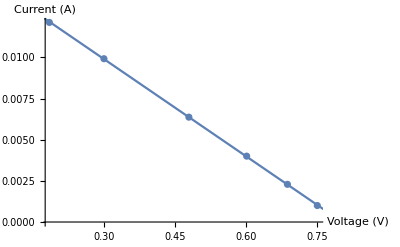

```mathematica
fit=LinearModelFit[voltCurr,x,x,Weights->1/(δV^2+δI^2)];
fit[{"BestFit","ParameterTable"}]
Ith=fit[[1,2,1]];
δVth=0.0001;
δIth=0.0000432552;
Vth=0.7994;
Rth=Vth/Ith;
δRth=Sqrt[(1/Ith δVth)^2+(-Vth/Ith^2 δIth)^2];
Rth "Ω" ± δRth "Ω"
Show[ErrorListPlot[Table[{{voltCurr[[i,1]],voltCurr[[i,2]]},ErrorBar[δV[[i]],δI[[i]]]},{i,1,Length[voltCurr]}]],Plot[fit[x],{x,0,3000}],AxesLabel->{"Voltage (V)","Current (A)"},ImageSize->Full]
```

Our theoretical value is just the one given on function generator which is 50 Ω (given without uncertainty). This is not quite within the error bounds for our experimentally determined value but is very close (the actual value is off by about 1%). This slight mismatch can probably be explained by the uncertainty of the function generator itself (a tolerance of 1% seems pretty standard for ohmic lab equipment).